# Scattered Acoustic Fields for different size regime

```mathematica
SetDirectory[NotebookDirectory[]]
```

## Beam coefficients

```mathematica
Gpw[l_,f_,z0_] =2*Sqrt[π]*Sqrt[2l+1] *ⅈ^l * Exp[(-ⅈ 2π f z0/cE)] ;
Gest[l_,f_,z0_] =2*Sqrt[(4π)(2l+1)]  Re[ⅈ^l Exp[(-ⅈ 2π f z0/cE)]] ; (*O coefficiente original estava errado, alterei para o correto*)
Gbes[l_,m_,β_,z0_,o_]=ⅈ^(l-m)Sqrt[(2l+1) 4π]Sqrt[((l-m)!)/((l+m)!)]LegendreP[l,m,Cos[β]]Exp[-ⅈ 2π f/cE Cos[β] z0]KroneckerDelta[o,m];
```

## Medium parameters

```mathematica
ρI= 997; (*water density*)
ρE= 1275/1000;(*air density*)
cI=1482;(*speed of sound in water*)
cE=34087/100;(*speed of sound in air*)
α =(ρI cI)/(ρE cE);
z=0;
NMax=160;
```

## Plane Wave

### Scattering Coefficient

```mathematica
DJ[l_,x_]=D[SphericalBesselJ[l,x],x];
DH[l_,x_]=D[SphericalHankelH1[l,x],x];
Clm[l_,f_,a_,z0_]:= Gpw[l,f,z0]( (α DJ[l,2π f /cE a]SphericalBesselJ[l,2π f /cI a]-SphericalBesselJ[l,2π f /cE a]DJ[l,2π f /cI a])/(SphericalHankelH1[l,2π f /cE a] DJ[l,2π f /cI a]-α SphericalBesselJ[l,2π f /cI a]DH[l,2π f /cE a]));(*Multipolo do Campo Espalhado*)
Alm[l_,f_,a_,z0_]:= Gpw[l,f,z0]( ( DH[l,2π f /cE a]SphericalBesselJ[l,2π f /cE a]-SphericalHankelH1[l,2π f /cE a]DJ[l,2π f /cE a])/(SphericalBesselJ[l,2π f /cI a] DH[l,2π f /cE a]- SphericalHankelH1[l,2π f /cE a]DJ[l,2π f /cI a]/α))  ;(*Multipolo do Campo Interno*)
Pesp[r_,θ_,ϕ_,f_,a_,z0_]:=Sum[SphericalHankelH1[l,2π f /cE r] SphericalHarmonicY[l,0,θ,ϕ] Clm[l,f,a,z0],{l,0,NMax}];
Pinc[r_,θ_,ϕ_,f_,z0_]:=Sum[SphericalBesselJ[l,2π f /cE r]SphericalHarmonicY[l,0,θ,ϕ] Gpw[l,f,z0],{l,0,NMax}]; 
PincExato[x_,y_,f_]=Exp[-ⅈ 2π f /cE x];
Pint[r_,θ_,ϕ_,f_,a_,z0_]:=Sum[SphericalBesselJ[l,2π f /cI r]SphericalHarmonicY[l,0,θ,ϕ] Alm[l,f,a,z0],{l,0,NMax}]; 
PTot[r_,θ_,ϕ_,f_,a_,z0_]:=Piecewise[{{Pint[r,θ,ϕ,f,a,z0],r<a},{Pesp[r,θ,ϕ,f,a,z0]+Pinc[r,θ,ϕ,f,z0],r≥a}}];
```

#### Grid Parameters

```mathematica
a1=14 10^(-5);
a2=14 10^(-4);
a3=14 10^(-3);
pontos=12;
f=40000;
samplePoints=3500;
```

#### Size Factors

```mathematica
ka1=2π f /cE a1;
ka2=2π f /cE a2;
ka3=2π f /cE a3;
```

## Calculations

```mathematica
GridXY1a=DeleteCases[Flatten[ParallelTable[{x,y},{x,-4 ka1,8ka1,ka1/pontos},{y,0,3 ka1,ka1/pontos}],1],{0,0}];
GridRT1=Select[DeleteCases[Flatten[ParallelTable[{r Cos[t],r Sin[t]},{r,0,8ka1,ka1/pontos},{t,0,2π,2π/30}],1],{0,0}],And[-4 ka1≤ #[[1]]≤ 8ka1,0≤ #[[2]]≤ 3ka1]&];
GridXY1=N[Union[GridXY1a,GridRT1]];
```

```mathematica
DadosTot1Semi=ParallelMap[Quiet[{(#[[1]])/ka1,(#[[2]])/ka1,Abs[PTot[Sqrt[#[[1]]^2+#[[2]]^2]/(2π f /cE ),ArcTan[#[[1]],#[[2]]],0,f,a1,z]]}]&,GridXY1];
```

```mathematica
DadosTot1All=Flatten[{{#[[1]],#[[2]],#[[3]]},{#[[1]],-#[[2]],#[[3]]}}&/@DadosTot1Semi,1];
```

```mathematica
GridXY2a=DeleteCases[Flatten[ParallelTable[{x,y},{x,-4 ka2,8ka2,ka2/pontos},{y,0,3 ka2,ka2/pontos}],1],{0,0}];
GridRT2=Select[DeleteCases[Flatten[ParallelTable[{r Cos[t],r Sin[t]},{r,0,8ka2,ka2/pontos},{t,0,2π,2π/30}],1],{0,0}],And[-4 ka2≤ #[[1]]≤ 8ka2,0≤ #[[2]]≤ 3ka2]&];
GridXY2=N[Union[GridXY2a,GridRT2]];
```

```mathematica
DadosTot2Semi=ParallelMap[Quiet[{(#[[1]])/ka2,(#[[2]])/ka2,Abs[PTot[Sqrt[#[[1]]^2+#[[2]]^2]/(2π f /cE ),ArcTan[#[[1]],#[[2]]],0,f,a2,z]]}]&,GridXY2];
```

```mathematica
DadosTot2All=Flatten[{{#[[1]],#[[2]],#[[3]]},{#[[1]],-#[[2]],#[[3]]}}&/@DadosTot2Semi,1];
```

```mathematica
GridXY3a=DeleteCases[Flatten[ParallelTable[{x,y},{x,-4 ka3,8ka3,ka3/pontos},{y,0,3 ka3,ka3/pontos}],1],{0,0}];
GridRT3=Select[DeleteCases[Flatten[ParallelTable[{r Cos[t],r Sin[t]},{r,0,8ka3,ka3/pontos},{t,0,2π,2π/30}],1],{0,0}],And[-4 ka3≤ #[[1]]≤ 8ka3,0≤ #[[2]]≤ 3ka3]&];
GridXY3=N[Union[GridXY3a,GridRT3]];
```

```mathematica
DadosTot3Semi=ParallelMap[Quiet[{(#[[1]])/ka3,(#[[2]])/ka3,Abs[PTot[Sqrt[#[[1]]^2+#[[2]]^2]/(2π f /cE ),ArcTan[#[[1]],#[[2]]],0,f,a3,z]]}]&,GridXY3];
```

```mathematica
DadosTot3All=Flatten[{{#[[1]],#[[2]],#[[3]]},{#[[1]],-#[[2]],#[[3]]}}&/@DadosTot3Semi,1];
```

```mathematica
GridXY2=RandomSample[DeleteCases[Flatten[ParallelTable[{x,y},{x,-4 ka2,8ka2,ka2/pontos},{y,-3 ka2,3 ka2,ka2/pontos}],1],{0,0}],samplePoints];
GridXY3=RandomSample[DeleteCases[Flatten[ParallelTable[{x,y},{x,-4 ka3,8ka3,ka3/pontos},{y,-3 ka3,3 ka3,ka3/pontos}],1],{0,0}],samplePoints];
```

```mathematica
LogDadosTot1={#[[1]],#[[2]],Log[#[[3]]]}&/@DadosTot1All;
LogDadosTot2={#[[1]],#[[2]],Log[#[[3]]]}&/@DadosTot2All;
LogDadosTot3={#[[1]],#[[2]],Log[#[[3]]]}&/@DadosTot3All;
```

```mathematica
Max1=Max[DadosTot1All[[All,3]],DadosTot2All[[All,3]],DadosTot3All[[All,3]]];
MaxLog1=Max[Log[DadosTot1All[[All,3]]+0.00001],Log[DadosTot2All[[All,3]]+0.00001],Log[DadosTot3All[[All,3]]+0.00001]];
```

```mathematica
NonNormalized
```

```mathematica
figTot1=Show[ListDensityPlot[DadosTot1All,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka1,0.1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
figTot2=Show[ListDensityPlot[DadosTot2All,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka2,1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
figTot3=Show[ListDensityPlot[DadosTot3All,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka3,1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
figLogTot1=Show[ListDensityPlot[LogDadosTot1,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka1,0.1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
figLogTot2=Show[ListDensityPlot[LogDadosTot2,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka2,1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
figLogTot3=Show[ListDensityPlot[LogDadosTot3,PlotRange->All,AspectRatio->Automatic,ImageSize->Large,LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],FrameStyle->LabelStyle->Directive[Black,FontFamily->"Helvetica",FontSize->20],ColorFunction->"DarkRainbow",InterpolationOrder->2,PerformanceGoal->"Quality",PlotTheme->"Detailed",PlotRangePadding->None,Frame->True,ColorFunctionScaling->True,FrameLabel->{"z (ka)","x (ka)"},PlotLegends->None],Graphics[{Black,Dashed, Thick,Circle[{0,0},1]}],Graphics[Text[Style["ka="<>ToString[Round[ka3,1]],FontFamily->"Helvetica",White,Bold,18],{7.9,2.5},{1,0}]]];
```

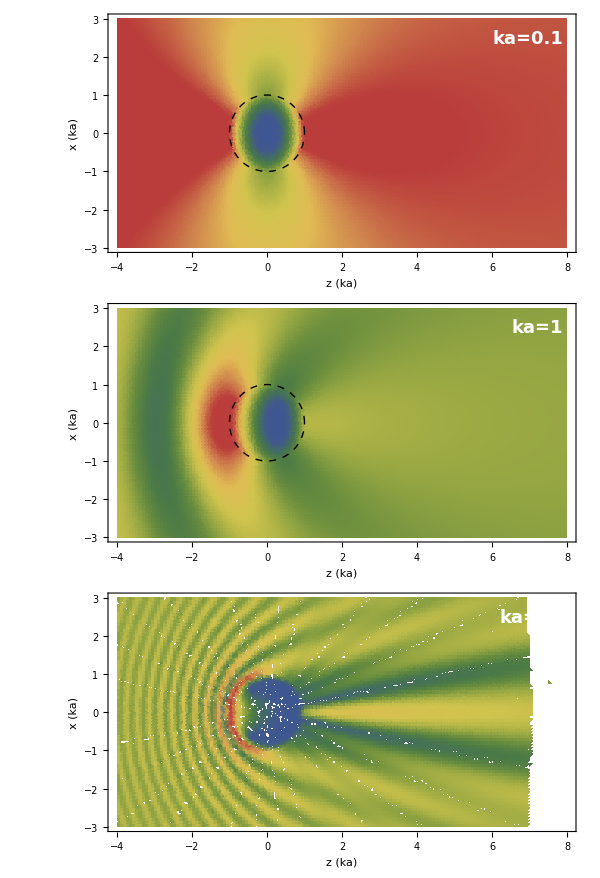

```mathematica
GraphicsGrid[{{figTot1},{figTot2},{figTot3}},ImageSize->600,Frame->None,Spacings->{-30, -10}]
```

```mathematica
comparacoes=Legended[GraphicsGrid[{{figTot1},{figTot2},{figTot3}},ImageSize->600,Frame->None,Spacings->{-30, -10}],Placed[BarLegend[{"DarkRainbow",{-1,1}},LegendMarkerSize->500,LegendLayout->"Row",Ticks->None],Below]]
```

-Graphics-

## Save

```mathematica
Export["Regimes.tiff",comparacoes,ImageSize->600,ImageResolution->500,"ImageEncoding"->"LZW"]
```

Regimes.tiff

```mathematica
Export["Regimes.png",comparacoes,ImageResolution->500]
```

Regimes.png